```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2"];
```

```mathematica
viewpoint={-1.785849751660347,-2.7180538166735624,0.9343040801371536}
```

```mathematica
dir="mc1e6_1sym_1snp_gamma\\";
filesamples="freq-1_1_gamma-";
```

```mathematica
mcmc=Import[dir<>filesamples<>"priorsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mcmc]
```

{1000000,2}

```mathematica
mpari=Exp@mcmc;
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
samplesi=Cases[samplesi(*[[;;;;Round[Length[samplesi]/100000]]]*),{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[samplesi]
```

999983

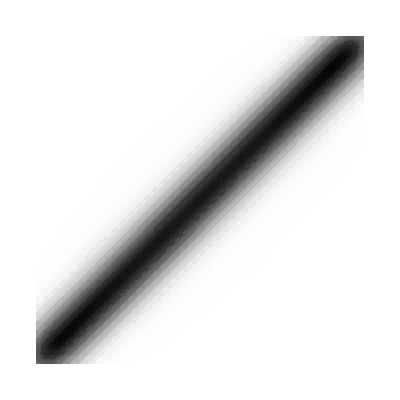

```mathematica
SmoothDensityHistogram[samplesi,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
viewpoint={-1.785849751660347,-2.7180538166735624,0.9343040801371536}
```

{-1.78585,-2.71805,0.934304}

```mathematica
plot=SmoothHistogram3D[samplesi(*[[;;;;1000]]*),Auto,"PDF",Mesh->5,ColorFunction->Function[{x,y,z},GrayLevel[1-z]],MeshStyle->red,PlotRange->{{0,1},{0,1},{0,All}},Axes->True,
ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},
ImageSize->a5rsize[[1]]*1.25,
AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate[

"p"[HoldForm[Subscript[f,s"|"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"g"] ]]

,Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["gamma_prior.png",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
(* cauchy prior *)
```

```mathematica
dir="testmc1e6_1sym_1snp_cauchy\\";
filesamples="freq-1_1_cauchy-";
```

```mathematica
mcmc=Import[dir<>filesamples<>"priorsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mcmc]
```

{1000000,2}

```mathematica
mpari=Exp@mcmc;
```

```mathematica
mpari=Import[dir<>filesamples<>"priorfsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mpari]
```

{1000000,2}

```mathematica
samplesi=mpari;
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
samplesi=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[samplesi]
```

70390

```mathematica
SmoothDensityHistogram[samplesi,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

$Aborted

```mathematica
plot=SmoothHistogram3D[samplesi,Auto,"PDF",Mesh->5,ColorFunction->Function[{x,y,z},GrayLevel[1-z]],MeshStyle->red,PlotRange->{{0,1},{0,1},{0,All}},Axes->True,
ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},
ImageSize->a5rsize[[1]]*1.25,
AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate[

"p"[HoldForm[Subscript[f,s"|"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"c"] ]]

,Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["cauchy_prior.png",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
Histogram3D[samplesi[[;;;;1000]],50,"PDF",(*ColorFunction->Function[z,GrayLevel[1-z]],*)PlotRange->{{0,1},{0,1},{0,All}},Axes->True,ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate["p"[HoldForm[Subscript[f,s" |"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"g"] ]],Pi/2,{1.25,0}]}]
```

-Graphics3D-